```mathematica
nw=500;
realdata = Import["wmax3_Ny15_Nx15_eta0.12_Ns40_ldostotal_with_mg.dat"];
Partition[realdata[[All,1]],12][[1,1]];
```

```mathematica
ldosawithmg=Table[{Partition[realdata[[All,1]],12][[i,1]],Total[Partition[Partition[realdata[[All,2]],12][[i]],6][[1]]]},{i,1,nw+1}];
ldosbwithmg=Table[{Partition[realdata[[All,1]],12][[i,1]],Total[Partition[Partition[realdata[[All,2]],12][[i]],6][[2]]]},{i,1,nw+1}];
realdatawomg = Import["wmax3_Ny15_Nx15_eta0.12_Ns40_ldostotal_wo_mg.dat"];
ldosdatwomg=Table[{Partition[realdatawomg[[All,1]],6][[i,1]],Total[Partition[realdatawomg[[All,2]],6][[i]]]},{i,1,nw+1}];
```

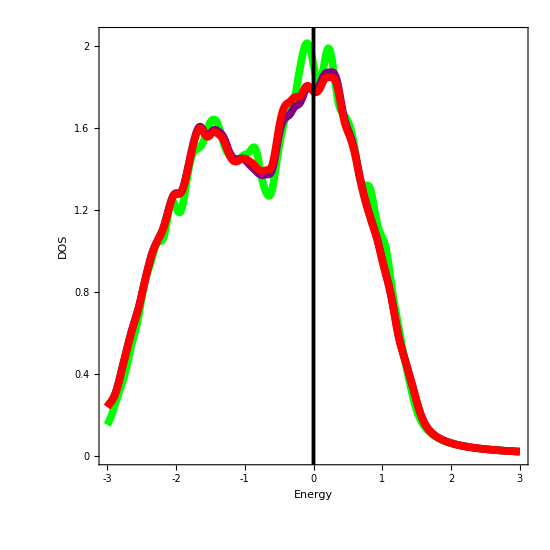

```mathematica
plot=ListPlot[{ldosdatwomg,ldosawithmg,ldosbwithmg},Joined->True,Frame->True,FrameStyle->Directive[Thickness[0.005],Black,45],PlotRange->{{-3,3},{0,2.05}},
FrameTicks->{{{{0,0,0.03},{0.4,0.4,0.03},{0.8,0.8,0.03},{1.2,1.2,0.03},{1.6,1.6,0.03},{2,2,0.03}},{{0,Null,0.03},{0.4,Null,0.03},{0.8,Null,0.03},{1.2,Null,0.03},{1.6,Null,0.03},{2,Null,0.03}}},{{{-3,-3,0.03},{-2,-2,0.03},{-1,-1,0.03},{0,0,0.03},{1,1,0.03},{2,2,0.03},{3,3,0.03}},{{-3,Null,0.03},{-2,Null,0.03},{-1,Null,0.03},{0,Null,0.03},{1,Null,0.03},{2,Null,0.03},{3,Null,0.03}}}},
GridLines->{{0},None},GridLinesStyle->Directive[Thickness[0.005],Black,50],FrameLabel->{{Style["DOS",40,FontFamily->"TimesNewRoman"],""},{Style["Energy",40,FontFamily->"TimesNewRoman"],""}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,25]},PlotStyle->{{Green,Thickness[0.01]},{Purple,Thickness[0.01]},{Red,Thickness[0.01]}},
ImagePadding->{{107,20},{112,8}},Axes->False,ImageSize->550,AspectRatio->1]
Export["plot.eps",plot];
```